```mathematica
ClearAll
```

ClearAll

```mathematica
cEinsteinmeV=65.1879672429008/1000;

n=100
H[x_,m_,omega2_,n_]:=-(1/(2 *m))*Laplacian[u[x],{x}]+ 0.5*m*omega2*x^2 u[x]
eige=NDEigensystem[{H[x,1,1,n]},u[x],{x,-50,50},n][[1]]
exact=Table[i+0.5,{i,0,n}]
error=Table[eige[[i]]/exact[[i]],{i,0,n}]
ListPlot[error]
```

100

NDEigensystem::maxeigen: A maximum number of 41 eigenvalues and functions can be computed for this discretized system.

{0.516525,3.47417,4.17146,13.0626,13.3312,28.7704,28.8258,50.6734,50.6896,78.7912,78.7939,113.179,113.179,153.791,153.791,200.678,200.678,253.791,253.791,313.178,313.178,378.79,378.79,450.677,450.677,528.79,528.79,613.177,613.177,703.786,703.786,800.642,800.642,903.63,903.63,1011.7,1011.7,1122.06,1122.06,1220.89,1220.89}

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5,40.5,41.5,42.5,43.5,44.5,45.5,46.5,47.5,48.5,49.5,50.5,51.5,52.5,53.5,54.5,55.5,56.5,57.5,58.5,59.5,60.5,61.5,62.5,63.5,64.5,65.5,66.5,67.5,68.5,69.5,70.5,71.5,72.5,73.5,74.5,75.5,76.5,77.5,78.5,79.5,80.5,81.5,82.5,83.5,84.5,85.5,86.5,87.5,88.5,89.5,90.5,91.5,92.5,93.5,94.5,95.5,96.5,97.5,98.5,99.5,100.5}

Part::partw: Part 42 of {0.516525,3.47417,4.17146,13.0626,13.3312,28.7704,28.8258,«27»,903.63,1011.7,1011.7,1122.06,1122.06,1220.89,1220.89} does not exist.

Part::partw: Part 43 of {0.516525,3.47417,4.17146,13.0626,13.3312,28.7704,28.8258,«27»,903.63,1011.7,1011.7,1122.06,1122.06,1220.89,1220.89} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

1/5

50

5

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5,40.5,41.5,42.5,43.5,44.5,45.5,46.5,47.5,48.5,49.5}

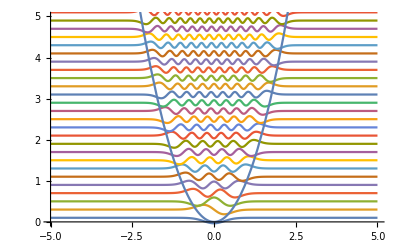

```mathematica
h=1/10;
Omega=1/5
M=50
B=5
V[x_,M_,Omega_]:=0.5*Omega*Omega*M*x^2
ℒ=-(1/(2M))*u''[x]+V[x,M,Omega]*u[x];
{vals,funs}=NDEigensystem[ℒ,u[x],{x,-B,B},50,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}];
vals/Omega
Show[Plot[Evaluate[(1/Sqrt[2M])*(funs)+vals],{x,-B,B}],Plot[V[x],{x,-B,B}],PlotRange->{{-B,B},{0,B}},AxesOrigin->{-B,0}]
```

31.5875

6

1

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5,40.5,41.5,42.5,43.5,44.5,45.5,46.5,47.5,48.5,49.5}

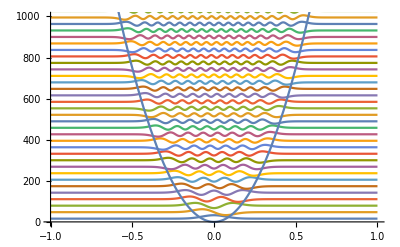

```mathematica
h=1/10;cEinsteinmeV=65.1879672429008/1000;
Omega=31.58754341976066
M=6
B=1
V[x_,M_,Omega_]:=0.5*Omega*Omega*M*x^2
ℒ=-(1/(2M))*u''[x]+V[x,M,Omega]*u[x];
{vals,funs}=NDEigensystem[ℒ,u[x],{x,-B,B},50,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}];
vals/Omega
Show[Plot[Evaluate[(6*funs)+vals],{x,-B,B}],Plot[V[x,M,Omega],{x,-B,B}],PlotRange->{{-B,B},{0,1000}},AxesOrigin->{-B,0}]
```

```mathematica
2
```

31.5875

12

1

2000

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5,40.5,41.5,42.5,43.5,44.5,45.5,46.5,47.5,48.5,49.5}

{0.479703,1.44184,2.40939,3.38227,4.3604,5.3437,6.33211,7.32553,8.32392,9.32719,10.3353,11.3482,12.3657,13.3879,14.4147,15.4461,16.4819,17.5221,18.5667,19.6157,20.6689,21.7264,22.788,23.8538,24.9237,25.9977,27.0757,28.1577,29.2436,30.3334,31.4272,32.5247,33.6261,34.7312,35.84,36.9526,38.0688,39.1887,40.3122,41.4393,42.5699,43.704,44.8417,45.9828,47.1273,48.2753,49.4266,50.5814,51.7394,52.9008}

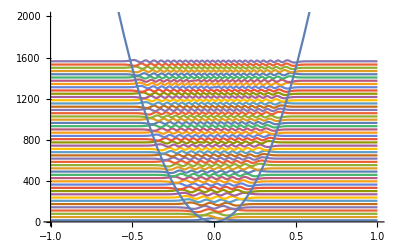

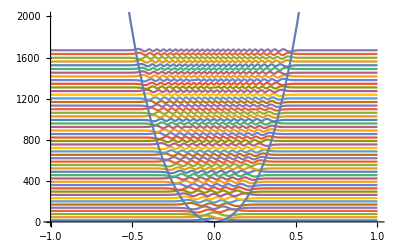

```mathematica
cEinsteinmeV=65.1879672429008/1000;
Omega=31.58754341976066
M=12
B=1
H=2000
V4Fit[x_]:=5478.867842258491*x*x+7678.83089846284*x*x*x*x
V[x_,M_,Omega_]:=0.5*Omega*Omega*M*x^2
ℒ1=-(1/(2M))*u''[x]+V[x,M,Omega]*u[x];
ℒ2=-(1/(2M))*u''[x]+V4Fit[x]*u[x];
{vals1,funs1}=NDEigensystem[ℒ1,u[x],{x,-B,B},50,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}];
f1=vals1/Omega
{vals2,funs2}=NDEigensystem[ℒ2,u[x],{x,-B,B},50,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}];
f2=vals2/Omega
Show[Plot[Evaluate[(6*funs1)+vals1],{x,-B,B}],Plot[V[x,M,Omega],{x,-B,B}],PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]
Show[Plot[Evaluate[(6*funs2)+vals2],{x,-B,B}],Plot[V4Fit[x],{x,-B,B}],PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]
```

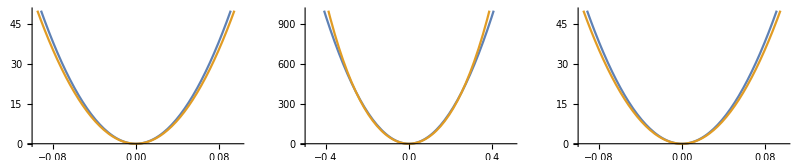

```mathematica
B=0.1;
H=50;
P1=Plot[{V[x,M,Omega],V4Fit[x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}];
B=0.5;
H=1000;
P2=Plot[{V[x,M,Omega],V4Fit[x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}];
B=0.75;
H=2000;
P3=Plot[{V[x,M,Omega],V4Fit[x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}];
GraphicsGrid[{{P1,P2,P1}},ImageSize->800]
```

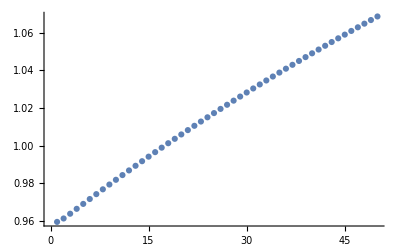

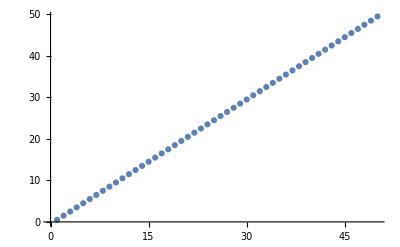

{0.959407,0.961226,0.963755,0.966363,0.968978,0.971583,0.97417,0.976738,0.979285,0.98181,0.984314,0.986796,0.989258,0.991699,0.994119,0.99652,0.998901,1.00126,1.00361,1.00593,1.00824,1.01053,1.0128,1.01506,1.01729,1.01952,1.02172,1.02392,1.02609,1.02825,1.0304,1.03253,1.03465,1.03675,1.03884,1.04092,1.04298,1.04503,1.04707,1.0491,1.05111,1.05311,1.0551,1.05708,1.05904,1.061,1.06294,1.06487,1.06679,1.0687}

```mathematica
ListPlot@Take[(f2/f1),50]
ListPlot@Take[f1,50]
Take[f2/f1,50]
```

```mathematica
Pcarbon=5.992
Pzriconium=8.249
H1[x_,P_]:=-1/(P*4) Laplacian[u[x],{x}]+ P*x^2 u[x]
NDEigensystem[{H1[x,Pcarbon]},u[x],{x,-10,10},20][[1]]
NDEigensystem[{H1[x,Pzriconium]},u[x],{x,-10,10},20][[1]]
```

5.992

8.249

{0.551592,2.04631,2.89165,6.86455,7.14144,14.3781,14.4314,24.9303,24.9432,38.3559,38.358,54.8897,54.8902,74.305,74.3051,96.8317,96.8317,122.239,122.239,150.759}

{0.53237,2.50294,3.22083,8.94139,9.18498,19.2967,19.3452,33.7797,33.7928,52.3073,52.3094,75.0271,75.0276,101.8,101.8,132.769,132.769,167.791,167.791,207.009}

```mathematica
H1[x_,P_]:=-0.25*1/P*Laplacian[u[x],{x}]+ P*x^2 u[x]
NDEigensystem[{H1[x,Pcarbon]},u[x],{x,-10,10},20][[1]]
NDEigensystem[{H1[x,Pzriconium]},u[x],{x,-10,10},20][[1]]
```

{0.551592,2.04631,2.89165,6.86455,7.14144,14.3781,14.4314,24.9303,24.9432,38.3559,38.358,54.8897,54.8902,74.305,74.3051,96.8317,96.8317,122.239,122.239,150.759}

{0.53237,2.50294,3.22083,8.94139,9.18498,19.2967,19.3452,33.7797,33.7928,52.3073,52.3094,75.0271,75.0276,101.8,101.8,132.769,132.769,167.791,167.791,207.009}

```mathematica
H1[x_,P_]:=-0.5*1/P*Laplacian[u[x],{x}]+ 0.5*P*x^2 u[x]
NDEigensystem[{H1[x,Pcarbon]},u[x],{x,-10,10},20][[1]]
NDEigensystem[{H1[x,Pzriconium]},u[x],{x,-10,10},20][[1]]
```

{0.545522,1.60362,2.86472,4.55059,5.31588,8.38024,8.57888,13.737,13.7714,20.3514,20.3568,28.6982,28.6991,38.3051,38.3053,49.6595,49.6595,62.2634,62.2634,76.6186}

{0.556173,1.73855,2.8275,5.31524,5.75148,10.4923,10.5784,17.8027,17.8201,26.9912,26.994,38.418,38.4185,51.7298,51.7299,67.2846,67.2847,84.7219,84.7219,104.403}

```mathematica
H1[x_,P_]:=-1/25*1/P*Laplacian[u[x],{x}]+ 10*P*x^2 u[x]
NDEigensystem[{H1[x,Pcarbon]},u[x],{x,-10,10},20][[1]]
NDEigensystem[{H1[x,Pzriconium]},u[x],{x,-10,10},20][[1]]
```

{1.2274,15.5115,17.6836,60.9452,61.9511,136.304,136.519,241.146,241.212,376.076,376.086,540.772,540.775,735.598,735.599,960.212,960.212,1214.96,1214.96,1499.49}

{1.62258,21.2976,24.2357,83.8201,85.1925,187.568,187.861,331.892,331.983,517.653,517.668,744.379,744.383,1012.6,1012.6,1321.81,1321.81,1672.52,1672.52,2064.22}

```mathematica
H1[x_,P_]:=-0.25*1/P*Laplacian[u[x],{x}]+ P*x^2 u[x]
NDEigensystem[{H1[x,1]},u[x],{x,-10,10},20][[1]]
NDEigensystem[{H1[x,1]},u[x],{x,-10,10},20][[1]]
```

{0.506512,1.50486,2.66281,3.56815,4.98464,6.15072,7.26832,8.66502,10.1338,11.5081,12.6739,14.2916,15.0807,17.645,17.8157,21.0921,21.1199,25.3867,25.3905,29.9699}

{0.506512,1.50486,2.66281,3.56815,4.98464,6.15072,7.26832,8.66502,10.1338,11.5081,12.6739,14.2916,15.0807,17.645,17.8157,21.0921,21.1199,25.3867,25.3905,29.9699}

```mathematica
H1[x_,P_]:=-0.5*1/P*Laplacian[u[x],{x}]+0.5* P*x^2 u[x]
NDEigensystem[{H1[x,1]},u[x],{x,-10,10},20][[1]]
NDEigensystem[{H1[x,1]},u[x],{x,-10,10},20][[1]]
```

{0.501189,1.50696,2.53003,3.53334,4.68703,5.53289,7.059,7.83234,9.11464,10.5335,11.508,12.6721,14.2015,15.5231,16.612,17.9303,19.4992,20.9359,22.14,23.4195}

{0.501189,1.50696,2.53003,3.53334,4.68703,5.53289,7.059,7.83234,9.11464,10.5335,11.508,12.6721,14.2015,15.5231,16.612,17.9303,19.4992,20.9359,22.14,23.4195}

```mathematica
H1[x_,P_]:=-1/P*Laplacian[u[x],{x}]+0.25* P*x^2 u[x]
NDEigensystem[{H1[x,1]},u[x],{x,-10,10},20][[1]]
NDEigensystem[{H1[x,1]},u[x],{x,-10,10},20][[1]]
```

{0.500306,1.50207,2.50714,3.51724,4.53404,5.55686,6.59465,7.61128,8.72652,9.60692,11.025,11.6228,13.4608,14.061,15.3392,16.8042,17.52,18.798,20.3324,21.1579}

{0.500306,1.50207,2.50714,3.51724,4.53404,5.55686,6.59465,7.61128,8.72652,9.60692,11.025,11.6228,13.4608,14.061,15.3392,16.8042,17.52,18.798,20.3324,21.1579}

```mathematica
{egnVal1,egnVec1}=NDEigensystem[{H[x]},u[x],{x,-10,10},20];
egnVal1
{egnVal2,egnVec2}=NDEigensystem[{H[x],DirichletCondition[u[x]==0,True]},u[x],{x,-10,10},20];
egnVal=Riffle[egnVal1,egnVal2]
```

{0.506512,0.506512,1.50486,1.50486,2.66281,2.66281,3.56815,3.56815,4.98464,4.98464,6.15072,6.15072,7.26832,7.26832,8.66502,8.66502,10.1338,10.1338,11.5081,11.5081,12.6739,12.6739,14.2916,14.2916,15.0807,15.0807,17.645,17.645,17.8157,17.8157,21.0921,21.0921,21.1199,21.1199,25.3867,25.3867,25.3905,25.3905,29.9699,29.9699}

{0.506512,0.501189,1.50486,1.50696,2.66281,2.53003,3.56815,3.53334,4.98464,4.68703,6.15072,5.53289,7.26832,7.059,8.66502,7.83234,10.1338,9.11464,11.5081,10.5335,12.6739,11.508,14.2916,12.6721,15.0807,14.2015,17.645,15.5231,17.8157,16.612,21.0921,17.9303,21.1199,19.4992,25.3867,20.9359,25.3905,22.14,29.9699,23.4195}